# Ixn params

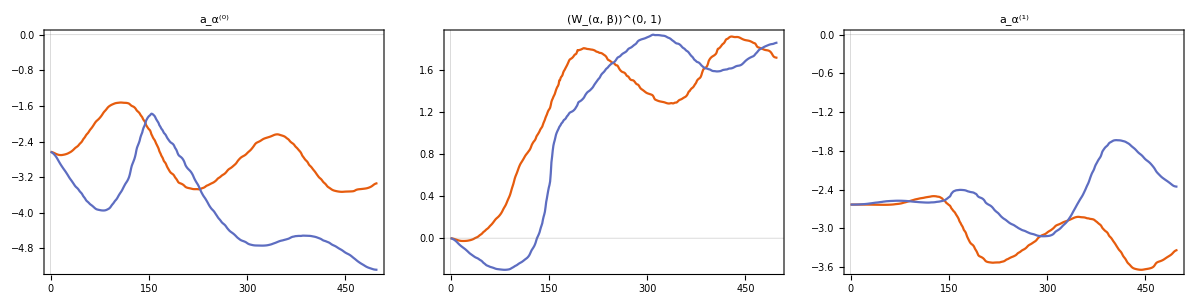

```mathematica
dataParams=Association[];
Do[
dataParams[ixn]=Import["../data/"<>dir<>"/ixn_params/"<>ixn<>"_"<>IntegerString[9800,10,5]<>".txt","Table"];
,{ixn,{"hX","hY","wXX1","wYY1","bX1","bY1"}}];
pltIxn=Grid[{{
ListLinePlot[{dataParams["hX"],dataParams["hY"]},PlotRange->All,ImageSize->250,PlotLabel->"a_α^(0)"],
ListLinePlot[{dataParams["wXX1"],dataParams["wYY1"]},PlotRange->All,ImageSize->250,PlotLabel->"(W_(α, β))^(0, 1)"],
ListLinePlot[{dataParams["bX1"],dataParams["bY1"]},PlotRange->All,ImageSize->250,PlotLabel->"a_α^(1)"]
}}]
```

```mathematica
leg=LineLegend[{ColorData[97,1],ColorData[97,2]},{"H","P"},LabelStyle->Directive[FontSize->20],LegendMarkerSize->40]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["figures"],CreateDirectory["figures"]];
Export["figures/ixns.pdf",pltIxn]
```

figures/ixns.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["figures"],CreateDirectory["figures"]];
Export["figures/ixns_leg.pdf",leg]
```

figures/ixns_leg.pdf

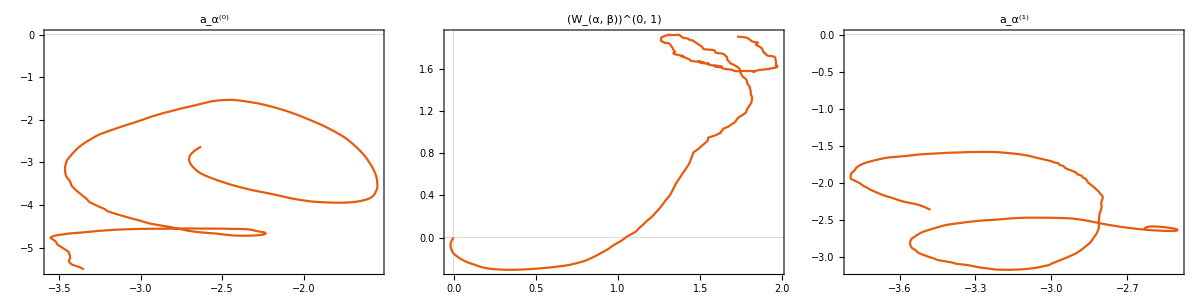

```mathematica
Module[
{ixns},
ixns=Association[];
Do[
ixns[ixn]=Import["../data/"<>dir<>"/ixn_params/"<>ixn<>"_"<>IntegerString[9800,10,5]<>".txt","Table"];
,{ixn,{"hX","hY","wXX1","wYY1","bX1","bY1"}}];
Grid[{{
ListLinePlot[Transpose[{ixns["hX"][[;;,2]],ixns["hY"][[;;,2]]}],PlotRange->All,ImageSize->250,PlotLabel->"a_α^(0)"],
ListLinePlot[Transpose[{ixns["wXX1"][[;;,2]],ixns["wYY1"][[;;,2]]}],PlotRange->All,ImageSize->250,PlotLabel->"(W_(α, β))^(0, 1)"],
ListLinePlot[Transpose[{ixns["bX1"][[;;,2]],ixns["bY1"][[;;,2]]}],PlotRange->All,ImageSize->250,PlotLabel->"a_α^(1)"]
}}]
]
```

# Moments

## Read visible

```mathematica
countsV=Association[];
Do[
countsV[timepoint]=Import["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/moments/moments.txt","Table"][[{1,2},2]];
,{timepoint,0,500-1}];
countsV=Values[countsV];
countsVLP=Transpose[{LowpassFilter[countsV[[;;,1]],0.1],LowpassFilter[countsV[[;;,2]],0.1]}];
```

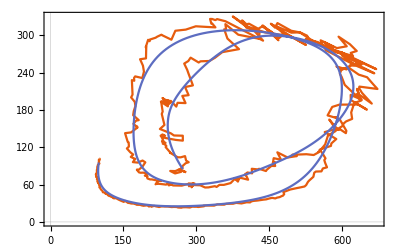

```mathematica
ListLinePlot[{countsV,countsVLP}]
```

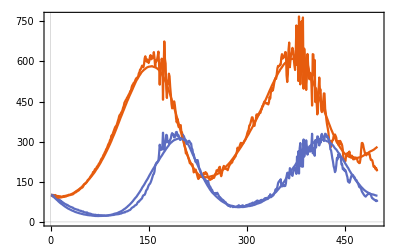

```mathematica
Show[ListLinePlot[Transpose[countsV]],pltMean2]
```

## Read hidden

```mathematica
countsH=Association[];
Do[
countsH[timepoint]=Import["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/moments/moments.txt","Table"][[{5,6},2]];
,{timepoint,0,500-1}];
countsH=Values[countsH];countsHLP=Transpose[{LowpassFilter[countsH[[;;,1]],0.1],LowpassFilter[countsH[[;;,2]],0.1]}];
```

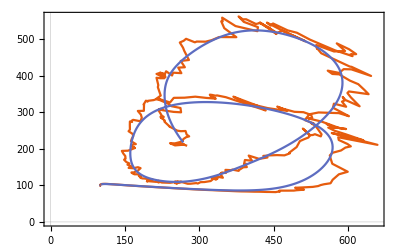

```mathematica
ListLinePlot[{countsH,countsHLP}]
```

# Time evolution of X moment

## Channels with derivatives

### Smooth params

```mathematica
SetDirectory[NotebookDirectory[]];

(* Import params *)
optStepRead=9800;
dataParams=Association[];
dataParamsLP=Association[];
Do[
dataParams[theta]=Import["../data/learn_params_rbm_centered/ixn_params/"<>theta<>"_"<>IntegerString[optStepRead,10,5]<>".txt","Table"][[;;,2]];
dataParamsLP[theta]=LowpassFilter[dataParams[theta],0.1];
,{theta,{"hX","hY","wXX1","wYY1","bX1","bY1"}}];

(* Import covs *)
dataCov=Association[];
Do[
dataCov[theta]={};
,{theta,{"hX","hY","wXX1","wYY1","bX1","bY1"}}];
Do[
tmp=Import["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/covs/hX.txt","Table"];
Do[
AppendTo[dataCov[tmp[[i,1]]],tmp[[i,2]]];
,{i,1,Length[tmp]}];
,{timepoint,0,500-1}];
dataCovLP=Association[];
Do[
dataCovLP[theta]=LowpassFilter[dataCov[theta],0.1];
,{theta,{"hX","hY","wXX1","wYY1","bX1","bY1"}}];

channels=Association[];
Do[
channels[theta]={};
,{theta,{"hX","hY","wXX1","wYY1","bX1","bY1"}}];

dt=0.01;
Do[
Do[
deriv=(dataParams[theta][[timepoint+2]]-dataParams[theta][[timepoint+1]])/dt;
AppendTo[channels[theta],dataCov[theta][[timepoint+1]]*deriv];
,{theta,{"hX","hY","wXX1","wYY1","bX1","bY1"}}];

,{timepoint,0,500-2}];
```

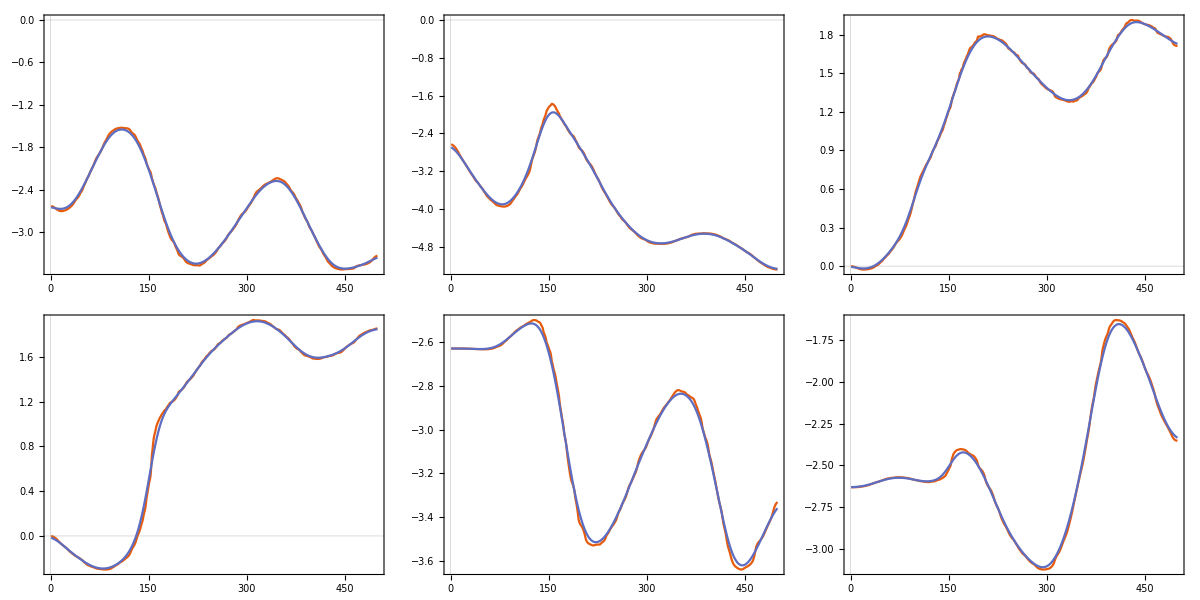

```mathematica
Grid[ArrayReshape[Table[ListLinePlot[{dataParams[theta],dataParamsLP[theta]},ImageSize->200],{theta,{"hX","hY","wXX1","wYY1","bX1","bY1"}}],{2,3}]]
```

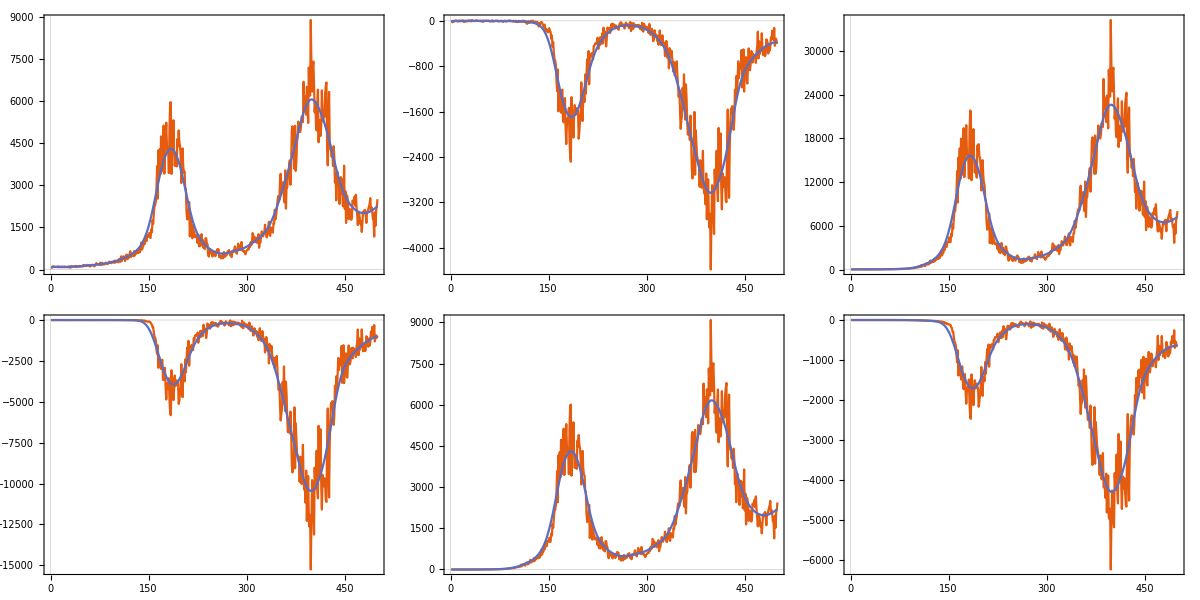

```mathematica
Grid[ArrayReshape[Table[ListLinePlot[{dataCov[theta],dataCovLP[theta]},ImageSize->200],{theta,{"hX","hY","wXX1","wYY1","bX1","bY1"}}],{2,3}]]
```

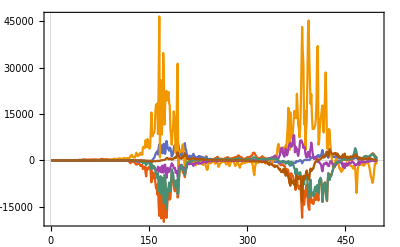

```mathematica
ListLinePlot[Values[channels],PlotRange->All]
```

```mathematica
channelsLP=Association[];
Do[
channelsLP[k]=LowpassFilter[channels[k],0.1];
,{k,Keys[channels]}];
```

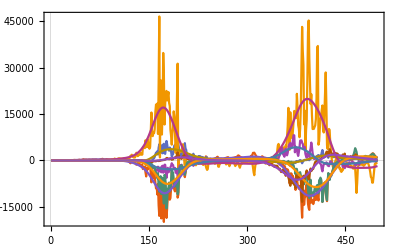

```mathematica
ListLinePlot[Join[Values[channels],Values[channelsLP]],PlotRange->All]
```

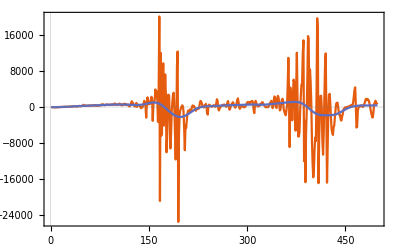

```mathematica
ListLinePlot[{Total[Values[channels]],Total[Values[channelsLP]]},PlotRange->All]
```

## True derivative

```mathematica
dt=0.01;
meanX={};
derivTrue={};
Do[
dataNext=Import["../data/sample_traj/"<>IntegerString[timepoint+1,10,4]<>"/moments/moments.txt","Table"];
dataThis=Import["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/moments/moments.txt","Table"];
AppendTo[derivTrue,(dataNext[[1,2]]-dataThis[[1,2]])/dt];
AppendTo[meanX,dataThis[[1,2]]];
,{timepoint,0,500-2}];
```

```mathematica
dt=0.01;
meanXLP=LowpassFilter[meanX,0.1];
derivTrueLP=(RotateLeft[meanXLP][[;;-2]]-meanXLP[[;;-2]])/dt;
```

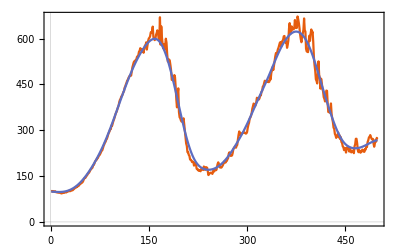

```mathematica
ListLinePlot[{meanX,meanXLP}]
```

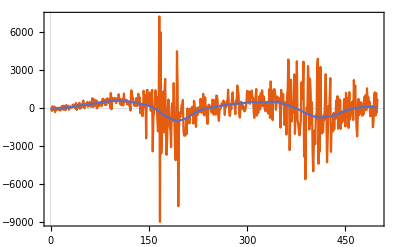

```mathematica
ListLinePlot[{derivTrue,derivTrueLP},PlotRange->All]
```

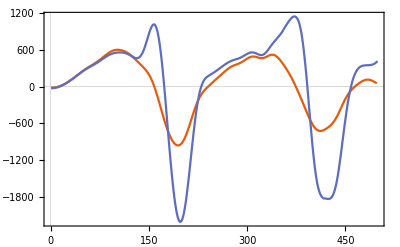

```mathematica
ListLinePlot[{derivTrueLP,Total[Values[channelsLP]]}]
```

# Legacy: calculate moments/covs

## Calculate and write out weight moments

```mathematica
SetDirectory[NotebookDirectory[]];
weightMoment=Association[];
weightMoment["wXX1"]=Association[];
weightMoment["wYY1"]=Association[];
Monitor[
Do[
weightMoment["wXX1"][timepoint]={};
weightMoment["wYY1"][timepoint]={};
Do[
data0=Import["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/layer_0_"<>IntegerString[sample,10,4]<>".txt","Table"];
data1=Transpose[Import["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/layer_1_"<>IntegerString[sample,10,4]<>".txt","Table"]];

data0X=conv[Select[data0,#[[3]]=="X"&]];
data0Y=conv[Select[data0,#[[3]]=="Y"&]];
data1X1=data1[[4]];
data1Y1=data1[[6]];

AppendTo[weightMoment["wXX1"][timepoint],data0X.adj.data1X1];
AppendTo[weightMoment["wYY1"][timepoint],data0Y.adj.data1Y1];

,{sample,0,100-1}];

weightMoment["wXX1"][timepoint]=Mean[weightMoment["wXX1"][timepoint]]//N;
weightMoment["wYY1"][timepoint]=Mean[weightMoment["wYY1"][timepoint]]//N;

f=OpenWrite["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/layer_0_1_moment.txt"];
Do[
WriteString[f,theta<>" "<>ToString@AccountingForm[weightMoment[theta][timepoint],{12,10},NumberSigns->{"-",""}]<>"\n"];
,{theta,{"wXX1","wYY1"}}];
Close[f];

,{timepoint,0,500-1}];
,ProgressIndicator[timepoint,{0,500-1}]]
```

## Calculate and Write Visible

```mathematica
SetDirectory[NotebookDirectory[]];
counts=Association[];
Monitor[
Do[
countsTmp={};
Do[
data=Import["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/layer_0_"<>IntegerString[sample,10,4]<>".txt","Table"];
AppendTo[countsTmp,{Length[Select[data,#[[3]]=="X"&]],Length[Select[data,#[[3]]=="Y"&]]}];
,{sample,0,100-1}];
counts[timepoint]=Mean[countsTmp]//N;

f=OpenWrite["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/layer_0_counts.txt"];
WriteString[f,"X "<>ToString[counts[timepoint][[1]]]<>"\n"];
WriteString[f,"Y "<>ToString[counts[timepoint][[2]]]];
Close[f];
,{timepoint,0,500-1}];
,ProgressIndicator[timepoint,{0,500-1}]]
```

## Calculate and Write Hidden

```mathematica
SetDirectory[NotebookDirectory[]];
counts=Association[];
Monitor[
Do[
countsTmp={};
Do[
data=Transpose[Import["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/layer_1_"<>IntegerString[sample,10,4]<>".txt","Table"]];
AppendTo[countsTmp,{Total[data[[4]]],Total[data[[6]]]}];
,{sample,0,100-1}];
counts[timepoint]=Mean[countsTmp]//N;

f=OpenWrite["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/layer_1_counts.txt"];
WriteString[f,"X1 "<>ToString[counts[timepoint][[1]]]<>"\n"];
WriteString[f,"Y1 "<>ToString[counts[timepoint][[2]]]];
Close[f];
,{timepoint,0,500-1}];
,ProgressIndicator[timepoint,{0,500-1}]]
```

## Adjacency matrix

```mathematica
boxLength=40;
adj={};
Do[
Do[
idx1=(i1-1)*boxLength+j1;

idx2=idx1;
AppendTo[adj,{idx1,idx2}->1];

i2=i1+1;
j2=j1+1;
If[i2>boxLength,i2=1];
If[j2>boxLength,j2=1];

idx2=(i2-1)*boxLength+j1;
AppendTo[adj,{idx1,idx2}->1];

idx2=(i1-1)*boxLength+j2;
AppendTo[adj,{idx1,idx2}->1];

idx2=(i2-1)*boxLength+j2;
AppendTo[adj,{idx1,idx2}->1];
,{j1,1,boxLength}];
,{i1,1,boxLength}];
adj=SparseArray[adj,{boxLength^2,boxLength^2}];
```

```mathematica
conv[dat_]:=Module[
{datC},
datC=Map[{(#[[1]]-1)*boxLength+#[[2]]}->1&,dat];
Return[SparseArray[datC,{boxLength^2}]];
];
```

## Calculate and write out the covs

```mathematica
SetDirectory[NotebookDirectory[]];
channels=Association[];
channels["hX"]=Association[];
channels["hY"]=Association[];
channels["wXX1"]=Association[];
channels["wYY1"]=Association[];
channels["bX1"]=Association[];
channels["bY1"]=Association[];
xSt=Association[];
Monitor[
Do[
cross=Association[];
cross["hX"]={};
cross["hY"]={};
cross["wXX1"]={};
cross["wYY1"]={};
cross["bX1"]={};
cross["bY1"]={};
means=Association[];
means["hX"]={};
means["hY"]={};
means["wXX1"]={};
means["wYY1"]={};
means["bX1"]={};
means["bY1"]={};
x={};
Do[
data0=Import["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/layer_0_"<>IntegerString[sample,10,4]<>".txt","Table"];
data1=Transpose[Import["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/layer_1_"<>IntegerString[sample,10,4]<>".txt","Table"]];

data0X=conv[Select[data0,#[[3]]=="X"&]];
data0Y=conv[Select[data0,#[[3]]=="Y"&]];
data1X1=data1[[4]];
data1Y1=data1[[6]];

AppendTo[means["hX"],Total[data0X]];
AppendTo[means["hY"],Total[data0Y]];
AppendTo[means["wXX1"],data0X.adj.data1X1];
AppendTo[means["wYY1"],data0Y.adj.data1Y1];
AppendTo[means["bX1"],Total[data1X1]];
AppendTo[means["bY1"],Total[data1Y1]];

AppendTo[x,means["hX"][[-1]]];

Do[
AppendTo[cross[theta],x[[-1]]*means[theta][[-1]]];
,{theta,{"hX","hY","wXX1","wYY1","bX1","bY1"}}];
,{sample,0,100-1}];

Do[
channels[theta][timepoint]=Mean[cross[theta]]-(Mean[means[theta]]*Mean[x])//N;
,{theta,{"hX","hY","wXX1","wYY1","bX1","bY1"}}];
xSt[timepoint]=Mean[x]//N;

f=OpenWrite["../data/learn_params/channel_covs/mean_X_"<>IntegerString[timepoint,10,4]<>".txt"];
Do[
WriteString[f,theta<>" "<>ToString@AccountingForm[channels[theta][timepoint],{12,10},NumberSigns->{"-",""}]<>"\n"];
,{theta,{"hX","hY","wXX1","wYY1","bX1","bY1"}}];
Close[f];

,{timepoint,0,500-1}];
,ProgressIndicator[timepoint,{0,500-1}]]
```